```mathematica
xexact[t_, n_,x0_,r0_,l_,g_]:=x0*Exp[-l*t]
```

```mathematica
yexact[t_, n_,x0_,r0_,l_,g_]:=If[l==g,
Exp[-l*t]((n-r0-x0)+l*x0*t),
l*(x0/(g-l))*Exp[-l*t]+((g*(n-r0-x0)-l*(n-r0))/(g-l))*Exp[-g*t]]
```

```mathematica
zexact[t_, n_,x0_,r0_,l_,g_]:=n-xexact[t, n,x0,r0,l,g]-yexact[t, n,x0,r0,l,g]
```

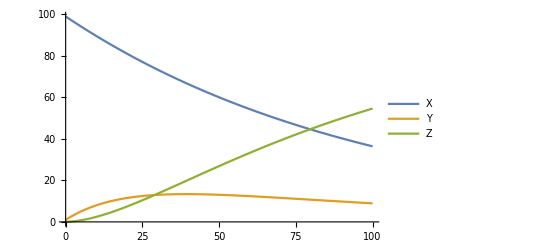

```mathematica
Plot[{xexact[t,100,99,0,0.1,0.05],yexact[t,100,99,0,0.1,0.05],zexact[t,100,99,0,0.1,0.05]},{t,0,100}, PlotLegends->{X,Y,Z}]
```

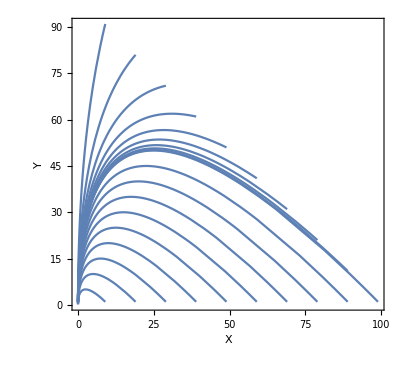

```mathematica
pplot = ParametricPlot[Flatten[{Table[{xexact[t,100,x0,0,0.1,0.05],yexact[t,100,x0,0,0.1,0.05]},{x0,9,99,10}],Table[{xexact[t,100,99-r0,r0,0.1,0.05],yexact[t,100,99-r0,r0,0.1,0.05]},{r0,10,90,10}]}],{t,0,100}, PlotRange->All, FrameLabel->{"X","Y"}, Frame->True]
```

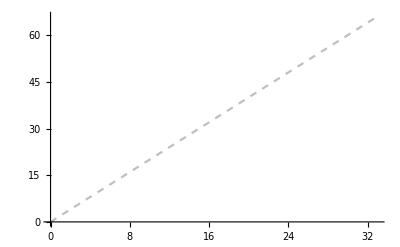

```mathematica
ymaxplot = Plot[2x,{x,0,33},PlotStyle->{Dashed, GrayLevel[0.75]}]
```

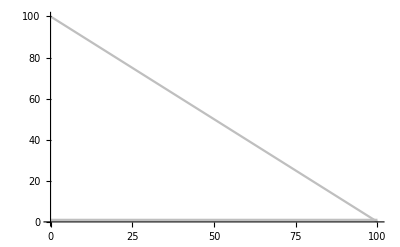

```mathematica
zoline = Plot[{1,100-x},{x,0,100},PlotStyle->GrayLevel[0.75]]
```

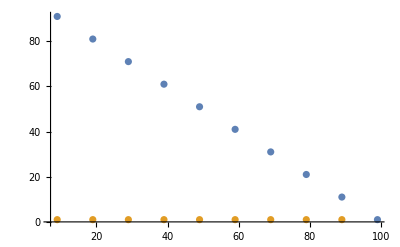

```mathematica
initpoints =ListPlot[{Table[{x0,100-x0},{x0,9,99,10}],Table[{99-r0,1},{r0,10,90,10}]},PlotRange->All ]
```

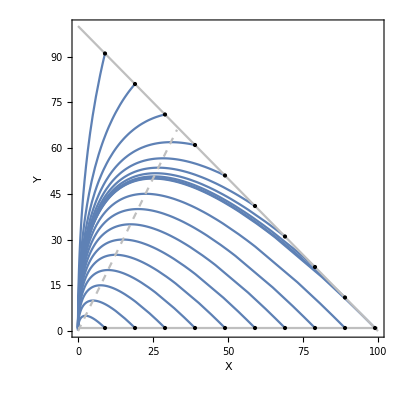

```mathematica
Show[pplot,ymaxplot,zoline,Graphics[{PointSize[1Medium],Point[Table[{x0,100-x0},{x0,9,99,10}]], Point[Table[{99-r0,1},{r0,10,90,10}]]}]]
```